```mathematica
texlis=ImageResize[ExampleData[{"ColorTexture",#},"Image"],{50,50}]&/@ExampleData["ColorTexture"][[All,2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ExampleData[{"Texture","Bricks"}]
```

-Graphics-

```mathematica
Manipulate[(*SeedRandom[13];*)
 Style[Overlay[
{Show[
Graphics3D[
{
Gray,Cuboid[{21,-100,-10},{19,-60,10}],
Gray,Cuboid[{19,-60,10},{40,-62,-10}],
Gray,Cuboid[{38,-62,-10},{40,-22,10}],
Gray,Cuboid[{38,-22,-10},{70,-24,10}],
Gray,Cuboid[{70,-22,10},{68,-78,-10}],
Gray,Cuboid[{70,-78,-10},{44,-76,10}],
Gray,Cuboid[{-40,-10,-10},{40,-12,10}]
}
],
      ContourPlot3D[
{
z==-10,
z==10
},
{x,-100,100},
{y,-100,100},
{z,-100,100},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Ash"}]],
Texture[ExampleData[{"ColorTexture","Ash"}]]
},
Mesh->False
],
 ContourPlot3D[
{
y==100,
y==-100,
x==100,
x==-100
},
{x,-100,100},
{y,-100,100},
{z,-11,11},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]]
},
Mesh->False
],
    Axes->False,
Boxed ->False,
     ViewAngle->
Dynamic[a],
     ViewVector->
Dynamic[
{
{
f[x, p⟦1⟧] Sin[v],
 Cos[v] f[x, p⟦1⟧], 
g[x, p⟦2⟧]
}, 
{
f[x, p⟦1⟧] Sin[v + π s⟦1⟧], 
Cos[v+π s⟦1⟧] f[x, p⟦1⟧], 
g[x, p⟦2⟧]+2 f[x, p⟦1⟧] Sin[1/2 π s⟦1⟧] Tan[1/2 π s⟦2⟧]
}
}
], 
ImageSize -> {480, 480}, 
     Lighting -> "Neutral"
],
 Graphics[{}, ImageSize -> {480, 480}]}], 
  Selectable -> False],
 {{t, "Metal4", ""}, 
  Rule @@@ Transpose[{ExampleData["ColorTexture"][[All, 2]], texlis}]},
 Delimiter,
 Item[
Control[
{{v, 0, Text[Style["move", Medium]]}, 0, Infinity, 
    ControlType -> Trigger, AnimationRate -> .5,
    AppearanceElements -> {"PlayPauseButton", 
      "FasterSlowerButtons"}}], Alignment -> Left],
 Delimiter,
 Column[{
   Item[Text[Style["zoom", Medium]], Alignment -> Left],
   Item[Control[{{a, π/2., ""}, 0.01, .99 π, 
      ImageSize -> Tiny}], Alignment -> Left]
   }],
 Delimiter,
 Column[{
   Item[Text[Style["look around", Medium]], Alignment -> Left],
   Item[Control[{{s, {.17, 0.}, ""}, {.001, -.999}, {2.999, .999}}], 
    Alignment -> Left]
   }],
 Delimiter,
 Column[{
   Item[Text[Style["shift around", Medium]], Alignment -> Left],
   Item[Control[{{p, {0., 0.}, ""},  {-100., -3.},{100.01, 3.}}], 
    Alignment -> Left]
   }],
 Delimiter,
 {{x, 0, ""}, {0 -> "subject", 1 -> "object"}},
 ControlPlacement -> Left, TrackedSymbols -> True, FrameMargins -> 0, 
 SynchronousUpdating -> False, SynchronousInitialization -> False,
 Initialization:>(f[x_, y_] := If[x == 0, y, 6.01 - y]; 
   g[x_, y_] := If[x == 0, y, -y];)]
```

```mathematica
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],
Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],
Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],
Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],
Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],
Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],
Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],
Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],
Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],
Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],
Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],
Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],
Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],
Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],
Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],
Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};
walledges = Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]
```

{{120,122},{1,41},{120,141},{39,41},{139,141},{39,79},{139,171},{77,79},{169,171},{23,79},{145,171},{23,25},{41,141},{101,103},{80,82},{1,26},{36,82},{24,26},{1,46},{74,76},{146,148},{151,200},{146,166},{151,153},{166,200},{169,171},{69,71},{141,200},{33,71},{141,143},{33,35},{141,171}}

```mathematica
walledges = Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]
```

{{120,122},{1,41},{120,141},{39,41},{139,141},{39,79},{139,171},{77,79},{169,171},{23,79},{145,171},{23,25},{41,141},{101,103},{80,82},{1,26},{36,82},{24,26},{1,46},{74,76},{146,148},{151,200},{146,166},{151,153},{166,201},{169,171},{69,71},{141,200},{33,71},{141,143},{33,35},{141,171}}

```mathematica
(*CreateDocument[*)
setMouse[expr_]:=MouseAppearance[expr,"Arrow"];
rotatevec[vec_,ang_]:=Module[
{x,y,z,newx,newy},
{x,y,z}=vec⟦2⟧;
newx=x*Cos@ang-y*Sin@ang;
newy=y*Cos@ang+x*Sin@ang;
{vec⟦1⟧,{newx,newy,z}}
];
DynamicModule[
{
px=100,
py=10,
pz=0,
viewd=0,
viewvector,
walls,
walledges,
fi,
checkbonds,
con1=1,
con2=1
},
viewvector=Dynamic@{{px,py-1,pz},{px,py,pz}};
walls={
Gray,Cuboid[{100+21+1,100-100+1,-10},{100+1+19,100-60+1,10}],
Gray,Cuboid[{100+1+19,100-60+1,10},{100+1+40,100-62+1,-10}],
Gray,Cuboid[{100+1+38,100-62+1,-10},{100+1+40,100-22+1,10}],
Gray,Cuboid[{100+1+38,100-22+1,-10},{100+1+70,100-24+1,10}],
Gray,Cuboid[{100+1+70,100-22+1,10},{100+1+68,100-78+1,-10}],
Gray,Cuboid[{100+1+70,100-78+1,-10},{100+1+44,100-76+1,10}],
Gray,Cuboid[{100-60+1,100+0+1,-10},{100+1+40,100+2+1,10}],
Gray,Cuboid[{100-19+1,100-100+1,-10},{100-21+1,100-75+1,10}],
Gray,Cuboid[{100-19+1,100-77+1,10},{100-65+1,100-75+1,-10}],
Gray,Cuboid[{100-100+1,100-25+1,10},{100-55+1,100-27+1,-10}],
Gray,Cuboid[{100+45+1,100+100,10},{100+47+1,100+50+1,-10}],
Gray,Cuboid[{100+45+1,100+52+1,10},{100+65+1,100+50+1,-10}],
Gray,Cuboid[{100+65+1,100+68+1,10},{100+100,100+70+1,-10}],
Gray,Cuboid[{100-30+1,100+100,10},{100-32+1,100+40+1,-10}],
Gray,Cuboid[{100-30+1,100+40+1,10},{100-68+1,100+42+1,-10}],
Gray,Cuboid[{100-68+1,100+40+1,10},{100-66+1,100+70+1,-10}]
};
walledges=Riffle[Sort/@Partition[First/@Catenate[List@@@walls⟦2;;;;2⟧],2],Sort/@Partition[Part[#,2]&/@Catenate[List@@@walls⟦2;;;;2⟧],2]]
~Join~
{{200,∞},{1,200},{-∞,1},{1,200},{1,200},{200,∞},{1,200},{-∞,1}};
fi[x_,y_,xpat_,ypat_]:=Between[x,xpat]&&Between[y,ypat];
checkbonds[{x_,y_,z_}]:=Module[
{},
Total[
Table[
Boole[
If[
fi[x,y,walledges⟦i⟧,walledges⟦i+1⟧],
True,
False
]
],
{i,1,Length@walledges,2}
]
]
];
EventHandler[
Show[
Graphics3D[
walls
],
Graphics3D[
{Green,Dynamic@Cuboid[{px,py,10},{px+2,py+2,11}]}
],
      ContourPlot3D[
{
z==-10,
z==10
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Ash"}]],
Texture[ExampleData[{"ColorTexture","Ash"}]]
},
Mesh->False
],
 ContourPlot3D[
{
y==200,
y==1,
x==200,
x==1
},
{x,1,200},
{y,1,200},
{z,-10,10},
ContourStyle->
{
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]],
Texture[ExampleData[{"ColorTexture","Kingwood"}]]
},
Mesh->False
],
ViewAngle->π/2,
ViewVector->viewvector,
ImageSize->Full
],
DynamicUpdating->True,
{
"RightArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧-{0,2,0}]==0,py-=2]),
"LeftArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{0,2,0}]==0&&checkbonds[viewvector⟦1,1⟧+{0,2,0}]==0,py+=2]),
"UpArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧+{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧+{2,0,0}]==0,px+=2]),
"DownArrowKeyDown":>(If[checkbonds[viewvector⟦1,2⟧-{2,0,0}]==0&&checkbonds[viewvector⟦1,1⟧-{2,0,0}]==0,px-=2]),
{"KeyDown","a"}:>(viewd+=2),
{"KeyDown","d"}:>(viewd-=2)
(*{"KeyDown","Space"}:>(pz+=0.1),
{"KeyDown","A"}:>(viewd+=π/12),
{"KeyDown","a"}:>(viewd+=π/2;con1=(Cos[viewd]*px- Sin[viewd]*py)/(px+$MachineEpsilon);con2=(py*Cos[viewd]+px*Sin[viewd])/(py+$MachineEpsilon)),
{"KeyDown","D"}:>(viewd-=π/12;con1=(Cos[viewd]*px- Sin[viewd]*py)/(px+$MachineEpsilon);con2=(py*Cos[viewd]+px*Sin[viewd])/(py+$MachineEpsilon)),
{"KeyDown","d"}:>(viewd-=π/12;con1=(Cos[viewd]*px- Sin[viewd]*py)/(px+$MachineEpsilon);con2=(py*Cos[viewd]+px*Sin[viewd])/(py+$MachineEpsilon))*)
}
]
]
(*,
CellMargins->0,ShowCellBracket->False,ShowCellLabel->False,"TrackCellChangeTimes"->False,WindowElements->{},WindowFrame->"Normal",WindowSize->Full,WindowMargins->Automatic,WindowTitle->"Mathematicraft",Background->Black,Editable->False,TextAlignment->Center,Deployed->True];*)
```

```mathematica
wal1=Range[#⟦1⟧,#⟦2⟧]&/@walledges;

wallcoords=Flatten[Table[{wal1⟦i,j⟧,wal1⟦i+1,k⟧},{i,1,Length@wal1,2},{j,Length@wal1⟦i⟧},{k,Length@wal1⟦i+1⟧}],2]
n=15;
Length@DeleteDuplicates[wallcoords]
SortBy[wallcoords,First];
```

{{120,1},{120,2},{120,3},{120,4},{120,5},{120,6},{120,7},{120,8},{120,9},{120,10},{120,11},{120,12},{120,13},{120,14},{120,15},{120,16},{120,17},{120,18},{120,19},{120,20},{120,21},{120,22},{120,23},{120,24},{120,25},{120,26},{120,27},{120,28},{120,29},{120,30},{120,31},{120,32},{120,33},{120,34},{120,35},{120,36},{120,37},{120,38},{120,39},{120,40},{120,41},{121,1},{121,2},{121,3},{121,4},{121,5},{121,6},{121,7},{121,8},{121,9},{121,10},{121,11},{121,12},{121,13},{121,14},{121,15},{121,16},{121,17},{121,18},{121,19},{121,20},{121,21},{121,22},{121,23},{121,24},{121,25},{121,26},{121,27},{121,28},{121,29},{121,30},{121,31},{121,32},{121,33},{121,34},{121,35},{121,36},{121,37},{121,38},{121,39},{121,40},{121,41},{122,1},{122,2},{122,3},{122,4},{122,5},{122,6},{122,7},{122,8},{122,9},{122,10},{122,11},{122,12},{122,13},{122,14},{122,15},{122,16},{122,17},{122,18},{122,19},{122,20},{122,21},{122,22},{122,23},{122,24},{122,25},{122,26},{122,27},{122,28},{122,29},{122,30},{122,31},{122,32},{122,33},{122,34},{122,35},{122,36},{122,37},{122,38},{122,39},{122,40},{122,41},{120,39},{120,40},{120,41},{121,39},{121,40},{121,41},{122,39},{122,40},{122,41},{123,39},{123,40},{123,41},{124,39},{124,40},{124,41},{125,39},{125,40},{125,41},{126,39},{126,40},{126,41},{127,39},{127,40},{127,41},{128,39},{128,40},{128,41},{129,39},{129,40},{129,41},{130,39},{130,40},{130,41},{131,39},{131,40},{131,41},{132,39},{132,40},{132,41},{133,39},{133,40},{133,41},{134,39},{134,40},{134,41},{135,39},{135,40},{135,41},{136,39},{136,40},{136,41},{137,39},{137,40},{137,41},{138,39},{138,40},{138,41},{139,39},{139,40},{139,41},{140,39},{140,40},{140,41},{141,39},{141,40},{141,41},{139,39},{139,40},{139,41},{139,42},{139,43},{139,44},{139,45},{139,46},{139,47},{139,48},{139,49},{139,50},{139,51},{139,52},{139,53},{139,54},{139,55},{139,56},{139,57},{139,58},{139,59},{139,60},{139,61},{139,62},{139,63},{139,64},{139,65},{139,66},{139,67},{139,68},{139,69},{139,70},{139,71},{139,72},{139,73},{139,74},{139,75},{139,76},{139,77},{139,78},{139,79},{140,39},{140,40},{140,41},{140,42},{140,43},{140,44},{140,45},{140,46},{140,47},{140,48},{140,49},{140,50},{140,51},{140,52},{140,53},{140,54},{140,55},{140,56},{140,57},{140,58},{140,59},{140,60},{140,61},{140,62},{140,63},{140,64},{140,65},{140,66},{140,67},{140,68},{140,69},{140,70},{140,71},{140,72},{140,73},{140,74},{140,75},{140,76},{140,77},{140,78},{140,79},{141,39},{141,40},{141,41},{141,42},{141,43},{141,44},{141,45},{141,46},{141,47},{141,48},{141,49},{141,50},{141,51},{141,52},{141,53},{141,54},{141,55},{141,56},{141,57},{141,58},{141,59},{141,60},{141,61},{141,62},{141,63},{141,64},{141,65},{141,66},{141,67},{141,68},{141,69},{141,70},{141,71},{141,72},{141,73},{141,74},{141,75},{141,76},{141,77},{141,78},{141,79},{139,77},{139,78},{139,79},{140,77},{140,78},{140,79},{141,77},{141,78},{141,79},{142,77},{142,78},{142,79},{143,77},{143,78},{143,79},{144,77},{144,78},{144,79},{145,77},{145,78},{145,79},{146,77},{146,78},{146,79},{147,77},{147,78},{147,79},{148,77},{148,78},{148,79},{149,77},{149,78},{149,79},{150,77},{150,78},{150,79},{151,77},{151,78},{151,79},{152,77},{152,78},{152,79},{153,77},{153,78},{153,79},{154,77},{154,78},{154,79},{155,77},{155,78},{155,79},{156,77},{156,78},{156,79},{157,77},{157,78},{157,79},{158,77},{158,78},{158,79},{159,77},{159,78},{159,79},{160,77},{160,78},{160,79},{161,77},{161,78},{161,79},{162,77},{162,78},{162,79},{163,77},{163,78},{163,79},{164,77},{164,78},{164,79},{165,77},{165,78},{165,79},{166,77},{166,78},{166,79},{167,77},{167,78},{167,79},{168,77},{168,78},{168,79},{169,77},{169,78},{169,79},{170,77},{170,78},{170,79},{171,77},{171,78},{171,79},{169,23},{169,24},{169,25},{169,26},{169,27},{169,28},{169,29},{169,30},{169,31},{169,32},{169,33},{169,34},{169,35},{169,36},{169,37},{169,38},{169,39},{169,40},{169,41},{169,42},{169,43},{169,44},{169,45},{169,46},{169,47},{169,48},{169,49},{169,50},{169,51},{169,52},{169,53},{169,54},{169,55},{169,56},{169,57},{169,58},{169,59},{169,60},{169,61},{169,62},{169,63},{169,64},{169,65},{169,66},{169,67},{169,68},{169,69},{169,70},{169,71},{169,72},{169,73},{169,74},{169,75},{169,76},{169,77},{169,78},{169,79},{170,23},{170,24},{170,25},{170,26},{170,27},{170,28},{170,29},{170,30},{170,31},{170,32},{170,33},{170,34},{170,35},{170,36},{170,37},{170,38},{170,39},{170,40},{170,41},{170,42},{170,43},{170,44},{170,45},{170,46},{170,47},{170,48},{170,49},{170,50},{170,51},{170,52},{170,53},{170,54},{170,55},{170,56},{170,57},{170,58},{170,59},{170,60},{170,61},{170,62},{170,63},{170,64},{170,65},{170,66},{170,67},{170,68},{170,69},{170,70},{170,71},{170,72},{170,73},{170,74},{170,75},{170,76},{170,77},{170,78},{170,79},{171,23},{171,24},{171,25},{171,26},{171,27},{171,28},{171,29},{171,30},{171,31},{171,32},{171,33},{171,34},{171,35},{171,36},{171,37},{171,38},{171,39},{171,40},{171,41},{171,42},{171,43},{171,44},{171,45},{171,46},{171,47},{171,48},{171,49},{171,50},{171,51},{171,52},{171,53},{171,54},{171,55},{171,56},{171,57},{171,58},{171,59},{171,60},{171,61},{171,62},{171,63},{171,64},{171,65},{171,66},{171,67},{171,68},{171,69},{171,70},{171,71},{171,72},{171,73},{171,74},{171,75},{171,76},{171,77},{171,78},{171,79},{145,23},{145,24},{145,25},{146,23},{146,24},{146,25},{147,23},{147,24},{147,25},{148,23},{148,24},{148,25},{149,23},{149,24},{149,25},{150,23},{150,24},{150,25},{151,23},{151,24},{151,25},{152,23},{152,24},{152,25},{153,23},{153,24},{153,25},{154,23},{154,24},{154,25},{155,23},{155,24},{155,25},{156,23},{156,24},{156,25},{157,23},{157,24},{157,25},{158,23},{158,24},{158,25},{159,23},{159,24},{159,25},{160,23},{160,24},{160,25},{161,23},{161,24},{161,25},{162,23},{162,24},{162,25},{163,23},{163,24},{163,25},{164,23},{164,24},{164,25},{165,23},{165,24},{165,25},{166,23},{166,24},{166,25},{167,23},{167,24},{167,25},{168,23},{168,24},{168,25},{169,23},{169,24},{169,25},{170,23},{170,24},{170,25},{171,23},{171,24},{171,25},{41,101},{41,102},{41,103},{42,101},{42,102},{42,103},{43,101},{43,102},{43,103},{44,101},{44,102},{44,103},{45,101},{45,102},{45,103},{46,101},{46,102},{46,103},{47,101},{47,102},{47,103},{48,101},{48,102},{48,103},{49,101},{49,102},{49,103},{50,101},{50,102},{50,103},{51,101},{51,102},{51,103},{52,101},{52,102},{52,103},{53,101},{53,102},{53,103},{54,101},{54,102},{54,103},{55,101},{55,102},{55,103},{56,101},{56,102},{56,103},{57,101},{57,102},{57,103},{58,101},{58,102},{58,103},{59,101},{59,102},{59,103},{60,101},{60,102},{60,103},{61,101},{61,102},{61,103},{62,101},{62,102},{62,103},{63,101},{63,102},{63,103},{64,101},{64,102},{64,103},{65,101},{65,102},{65,103},{66,101},{66,102},{66,103},{67,101},{67,102},{67,103},{68,101},{68,102},{68,103},{69,101},{69,102},{69,103},{70,101},{70,102},{70,103},{71,101},{71,102},{71,103},{72,101},{72,102},{72,103},{73,101},{73,102},{73,103},{74,101},{74,102},{74,103},{75,101},{75,102},{75,103},{76,101},{76,102},{76,103},{77,101},{77,102},{77,103},{78,101},{78,102},{78,103},{79,101},{79,102},{79,103},{80,101},{80,102},{80,103},{81,101},{81,102},{81,103},{82,101},{82,102},{82,103},{83,101},{83,102},{83,103},{84,101},{84,102},{84,103},{85,101},{85,102},{85,103},{86,101},{86,102},{86,103},{87,101},{87,102},{87,103},{88,101},{88,102},{88,103},{89,101},{89,102},{89,103},{90,101},{90,102},{90,103},{91,101},{91,102},{91,103},{92,101},{92,102},{92,103},{93,101},{93,102},{93,103},{94,101},{94,102},{94,103},{95,101},{95,102},{95,103},{96,101},{96,102},{96,103},{97,101},{97,102},{97,103},{98,101},{98,102},{98,103},{99,101},{99,102},{99,103},{100,101},{100,102},{100,103},{101,101},{101,102},{101,103},{102,101},{102,102},{102,103},{103,101},{103,102},{103,103},{104,101},{104,102},{104,103},{105,101},{105,102},{105,103},{106,101},{106,102},{106,103},{107,101},{107,102},{107,103},{108,101},{108,102},{108,103},{109,101},{109,102},{109,103},{110,101},{110,102},{110,103},{111,101},{111,102},{111,103},{112,101},{112,102},{112,103},{113,101},{113,102},{113,103},{114,101},{114,102},{114,103},{115,101},{115,102},{115,103},{116,101},{116,102},{116,103},{117,101},{117,102},{117,103},{118,101},{118,102},{118,103},{119,101},{119,102},{119,103},{120,101},{120,102},{120,103},{121,101},{121,102},{121,103},{122,101},{122,102},{122,103},{123,101},{123,102},{123,103},{124,101},{124,102},{124,103},{125,101},{125,102},{125,103},{126,101},{126,102},{126,103},{127,101},{127,102},{127,103},{128,101},{128,102},{128,103},{129,101},{129,102},{129,103},{130,101},{130,102},{130,103},{131,101},{131,102},{131,103},{132,101},{132,102},{132,103},{133,101},{133,102},{133,103},{134,101},{134,102},{134,103},{135,101},{135,102},{135,103},{136,101},{136,102},{136,103},{137,101},{137,102},{137,103},{138,101},{138,102},{138,103},{139,101},{139,102},{139,103},{140,101},{140,102},{140,103},{141,101},{141,102},{141,103},{80,1},{80,2},{80,3},{80,4},{80,5},{80,6},{80,7},{80,8},{80,9},{80,10},{80,11},{80,12},{80,13},{80,14},{80,15},{80,16},{80,17},{80,18},{80,19},{80,20},{80,21},{80,22},{80,23},{80,24},{80,25},{80,26},{81,1},{81,2},{81,3},{81,4},{81,5},{81,6},{81,7},{81,8},{81,9},{81,10},{81,11},{81,12},{81,13},{81,14},{81,15},{81,16},{81,17},{81,18},{81,19},{81,20},{81,21},{81,22},{81,23},{81,24},{81,25},{81,26},{82,1},{82,2},{82,3},{82,4},{82,5},{82,6},{82,7},{82,8},{82,9},{82,10},{82,11},{82,12},{82,13},{82,14},{82,15},{82,16},{82,17},{82,18},{82,19},{82,20},{82,21},{82,22},{82,23},{82,24},{82,25},{82,26},{36,24},{36,25},{36,26},{37,24},{37,25},{37,26},{38,24},{38,25},{38,26},{39,24},{39,25},{39,26},{40,24},{40,25},{40,26},{41,24},{41,25},{41,26},{42,24},{42,25},{42,26},{43,24},{43,25},{43,26},{44,24},{44,25},{44,26},{45,24},{45,25},{45,26},{46,24},{46,25},{46,26},{47,24},{47,25},{47,26},{48,24},{48,25},{48,26},{49,24},{49,25},{49,26},{50,24},{50,25},{50,26},{51,24},{51,25},{51,26},{52,24},{52,25},{52,26},{53,24},{53,25},{53,26},{54,24},{54,25},{54,26},{55,24},{55,25},{55,26},{56,24},{56,25},{56,26},{57,24},{57,25},{57,26},{58,24},{58,25},{58,26},{59,24},{59,25},{59,26},{60,24},{60,25},{60,26},{61,24},{61,25},{61,26},{62,24},{62,25},{62,26},{63,24},{63,25},{63,26},{64,24},{64,25},{64,26},{65,24},{65,25},{65,26},{66,24},{66,25},{66,26},{67,24},{67,25},{67,26},{68,24},{68,25},{68,26},{69,24},{69,25},{69,26},{70,24},{70,25},{70,26},{71,24},{71,25},{71,26},{72,24},{72,25},{72,26},{73,24},{73,25},{73,26},{74,24},{74,25},{74,26},{75,24},{75,25},{75,26},{76,24},{76,25},{76,26},{77,24},{77,25},{77,26},{78,24},{78,25},{78,26},{79,24},{79,25},{79,26},{80,24},{80,25},{80,26},{81,24},{81,25},{81,26},{82,24},{82,25},{82,26},{1,74},{1,75},{1,76},{2,74},{2,75},{2,76},{3,74},{3,75},{3,76},{4,74},{4,75},{4,76},{5,74},{5,75},{5,76},{6,74},{6,75},{6,76},{7,74},{7,75},{7,76},{8,74},{8,75},{8,76},{9,74},{9,75},{9,76},{10,74},{10,75},{10,76},{11,74},{11,75},{11,76},{12,74},{12,75},{12,76},{13,74},{13,75},{13,76},{14,74},{14,75},{14,76},{15,74},{15,75},{15,76},{16,74},{16,75},{16,76},{17,74},{17,75},{17,76},{18,74},{18,75},{18,76},{19,74},{19,75},{19,76},{20,74},{20,75},{20,76},{21,74},{21,75},{21,76},{22,74},{22,75},{22,76},{23,74},{23,75},{23,76},{24,74},{24,75},{24,76},{25,74},{25,75},{25,76},{26,74},{26,75},{26,76},{27,74},{27,75},{27,76},{28,74},{28,75},{28,76},{29,74},{29,75},{29,76},{30,74},{30,75},{30,76},{31,74},{31,75},{31,76},{32,74},{32,75},{32,76},{33,74},{33,75},{33,76},{34,74},{34,75},{34,76},{35,74},{35,75},{35,76},{36,74},{36,75},{36,76},{37,74},{37,75},{37,76},{38,74},{38,75},{38,76},{39,74},{39,75},{39,76},{40,74},{40,75},{40,76},{41,74},{41,75},{41,76},{42,74},{42,75},{42,76},{43,74},{43,75},{43,76},{44,74},{44,75},{44,76},{45,74},{45,75},{45,76},{46,74},{46,75},{46,76},{146,151},{146,152},{146,153},{146,154},{146,155},{146,156},{146,157},{146,158},{146,159},{146,160},{146,161},{146,162},{146,163},{146,164},{146,165},{146,166},{146,167},{146,168},{146,169},{146,170},{146,171},{146,172},{146,173},{146,174},{146,175},{146,176},{146,177},{146,178},{146,179},{146,180},{146,181},{146,182},{146,183},{146,184},{146,185},{146,186},{146,187},{146,188},{146,189},{146,190},{146,191},{146,192},{146,193},{146,194},{146,195},{146,196},{146,197},{146,198},{146,199},{146,200},{147,151},{147,152},{147,153},{147,154},{147,155},{147,156},{147,157},{147,158},{147,159},{147,160},{147,161},{147,162},{147,163},{147,164},{147,165},{147,166},{147,167},{147,168},{147,169},{147,170},{147,171},{147,172},{147,173},{147,174},{147,175},{147,176},{147,177},{147,178},{147,179},{147,180},{147,181},{147,182},{147,183},{147,184},{147,185},{147,186},{147,187},{147,188},{147,189},{147,190},{147,191},{147,192},{147,193},{147,194},{147,195},{147,196},{147,197},{147,198},{147,199},{147,200},{148,151},{148,152},{148,153},{148,154},{148,155},{148,156},{148,157},{148,158},{148,159},{148,160},{148,161},{148,162},{148,163},{148,164},{148,165},{148,166},{148,167},{148,168},{148,169},{148,170},{148,171},{148,172},{148,173},{148,174},{148,175},{148,176},{148,177},{148,178},{148,179},{148,180},{148,181},{148,182},{148,183},{148,184},{148,185},{148,186},{148,187},{148,188},{148,189},{148,190},{148,191},{148,192},{148,193},{148,194},{148,195},{148,196},{148,197},{148,198},{148,199},{148,200},{146,151},{146,152},{146,153},{147,151},{147,152},{147,153},{148,151},{148,152},{148,153},{149,151},{149,152},{149,153},{150,151},{150,152},{150,153},{151,151},{151,152},{151,153},{152,151},{152,152},{152,153},{153,151},{153,152},{153,153},{154,151},{154,152},{154,153},{155,151},{155,152},{155,153},{156,151},{156,152},{156,153},{157,151},{157,152},{157,153},{158,151},{158,152},{158,153},{159,151},{159,152},{159,153},{160,151},{160,152},{160,153},{161,151},{161,152},{161,153},{162,151},{162,152},{162,153},{163,151},{163,152},{163,153},{164,151},{164,152},{164,153},{165,151},{165,152},{165,153},{166,151},{166,152},{166,153},{166,169},{166,170},{166,171},{167,169},{167,170},{167,171},{168,169},{168,170},{168,171},{169,169},{169,170},{169,171},{170,169},{170,170},{170,171},{171,169},{171,170},{171,171},{172,169},{172,170},{172,171},{173,169},{173,170},{173,171},{174,169},{174,170},{174,171},{175,169},{175,170},{175,171},{176,169},{176,170},{176,171},{177,169},{177,170},{177,171},{178,169},{178,170},{178,171},{179,169},{179,170},{179,171},{180,169},{180,170},{180,171},{181,169},{181,170},{181,171},{182,169},{182,170},{182,171},{183,169},{183,170},{183,171},{184,169},{184,170},{184,171},{185,169},{185,170},{185,171},{186,169},{186,170},{186,171},{187,169},{187,170},{187,171},{188,169},{188,170},{188,171},{189,169},{189,170},{189,171},{190,169},{190,170},{190,171},{191,169},{191,170},{191,171},{192,169},{192,170},{192,171},{193,169},{193,170},{193,171},{194,169},{194,170},{194,171},{195,169},{195,170},{195,171},{196,169},{196,170},{196,171},{197,169},{197,170},{197,171},{198,169},{198,170},{198,171},{199,169},{199,170},{199,171},{200,169},{200,170},{200,171},{69,141},{69,142},{69,143},{69,144},{69,145},{69,146},{69,147},{69,148},{69,149},{69,150},{69,151},{69,152},{69,153},{69,154},{69,155},{69,156},{69,157},{69,158},{69,159},{69,160},{69,161},{69,162},{69,163},{69,164},{69,165},{69,166},{69,167},{69,168},{69,169},{69,170},{69,171},{69,172},{69,173},{69,174},{69,175},{69,176},{69,177},{69,178},{69,179},{69,180},{69,181},{69,182},{69,183},{69,184},{69,185},{69,186},{69,187},{69,188},{69,189},{69,190},{69,191},{69,192},{69,193},{69,194},{69,195},{69,196},{69,197},{69,198},{69,199},{69,200},{70,141},{70,142},{70,143},{70,144},{70,145},{70,146},{70,147},{70,148},{70,149},{70,150},{70,151},{70,152},{70,153},{70,154},{70,155},{70,156},{70,157},{70,158},{70,159},{70,160},{70,161},{70,162},{70,163},{70,164},{70,165},{70,166},{70,167},{70,168},{70,169},{70,170},{70,171},{70,172},{70,173},{70,174},{70,175},{70,176},{70,177},{70,178},{70,179},{70,180},{70,181},{70,182},{70,183},{70,184},{70,185},{70,186},{70,187},{70,188},{70,189},{70,190},{70,191},{70,192},{70,193},{70,194},{70,195},{70,196},{70,197},{70,198},{70,199},{70,200},{71,141},{71,142},{71,143},{71,144},{71,145},{71,146},{71,147},{71,148},{71,149},{71,150},{71,151},{71,152},{71,153},{71,154},{71,155},{71,156},{71,157},{71,158},{71,159},{71,160},{71,161},{71,162},{71,163},{71,164},{71,165},{71,166},{71,167},{71,168},{71,169},{71,170},{71,171},{71,172},{71,173},{71,174},{71,175},{71,176},{71,177},{71,178},{71,179},{71,180},{71,181},{71,182},{71,183},{71,184},{71,185},{71,186},{71,187},{71,188},{71,189},{71,190},{71,191},{71,192},{71,193},{71,194},{71,195},{71,196},{71,197},{71,198},{71,199},{71,200},{33,141},{33,142},{33,143},{34,141},{34,142},{34,143},{35,141},{35,142},{35,143},{36,141},{36,142},{36,143},{37,141},{37,142},{37,143},{38,141},{38,142},{38,143},{39,141},{39,142},{39,143},{40,141},{40,142},{40,143},{41,141},{41,142},{41,143},{42,141},{42,142},{42,143},{43,141},{43,142},{43,143},{44,141},{44,142},{44,143},{45,141},{45,142},{45,143},{46,141},{46,142},{46,143},{47,141},{47,142},{47,143},{48,141},{48,142},{48,143},{49,141},{49,142},{49,143},{50,141},{50,142},{50,143},{51,141},{51,142},{51,143},{52,141},{52,142},{52,143},{53,141},{53,142},{53,143},{54,141},{54,142},{54,143},{55,141},{55,142},{55,143},{56,141},{56,142},{56,143},{57,141},{57,142},{57,143},{58,141},{58,142},{58,143},{59,141},{59,142},{59,143},{60,141},{60,142},{60,143},{61,141},{61,142},{61,143},{62,141},{62,142},{62,143},{63,141},{63,142},{63,143},{64,141},{64,142},{64,143},{65,141},{65,142},{65,143},{66,141},{66,142},{66,143},{67,141},{67,142},{67,143},{68,141},{68,142},{68,143},{69,141},{69,142},{69,143},{70,141},{70,142},{70,143},{71,141},{71,142},{71,143},{33,141},{33,142},{33,143},{33,144},{33,145},{33,146},{33,147},{33,148},{33,149},{33,150},{33,151},{33,152},{33,153},{33,154},{33,155},{33,156},{33,157},{33,158},{33,159},{33,160},{33,161},{33,162},{33,163},{33,164},{33,165},{33,166},{33,167},{33,168},{33,169},{33,170},{33,171},{34,141},{34,142},{34,143},{34,144},{34,145},{34,146},{34,147},{34,148},{34,149},{34,150},{34,151},{34,152},{34,153},{34,154},{34,155},{34,156},{34,157},{34,158},{34,159},{34,160},{34,161},{34,162},{34,163},{34,164},{34,165},{34,166},{34,167},{34,168},{34,169},{34,170},{34,171},{35,141},{35,142},{35,143},{35,144},{35,145},{35,146},{35,147},{35,148},{35,149},{35,150},{35,151},{35,152},{35,153},{35,154},{35,155},{35,156},{35,157},{35,158},{35,159},{35,160},{35,161},{35,162},{35,163},{35,164},{35,165},{35,166},{35,167},{35,168},{35,169},{35,170},{35,171}}

1950

```mathematica
Length[Select[Range[40000],!MemberQ[wallcoords,{Quotient[#,n]+1,Mod[#,n]}]&]]
```

39916

```mathematica
Length@Intersection[Table[{Quotient[i,200]+1,Mod[i,200]},{i,40000}],wallcoords]
```

1944

```mathematica
Do[readmap⟦i,j⟧=0,{i,walledges⟦k,1⟧,walledges⟦k,2⟧},{j,walledges⟦k+1,1⟧,walledges⟦k+1,2⟧},{k,1,Length@walledges,2}]
```

```mathematica
Array
```

```mathematica
readmap
```

```mathematica
findway[10,10,100,100]
```

```mathematica
cmap;
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

15

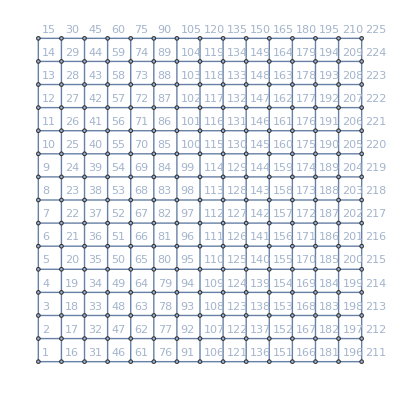

Root::nup: {Mod[z,15]==6,Quotient[z,15]==7} is not a univariate polynomial.

Root[{Mod[z,15]==6,Quotient[z,15]==7},z]

Quotient[z,15]

```mathematica
n=15
GridGraph[{n,n},VertexLabels->Automatic]
Clear[z]
Solve[{Mod[z,n]==6,Quotient[z,n]==7},z]
y=Quotient[z,n]
```

```mathematica
Mod[82,15]
```

7

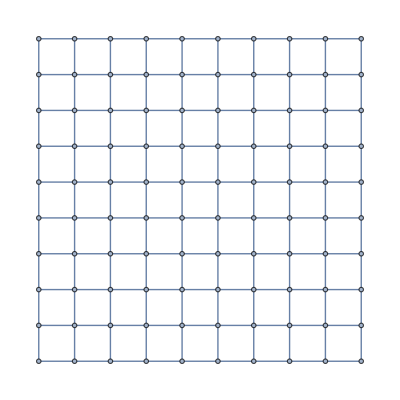

{1,2,3,4,5,6,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

{1<->2,1<->11,2<->3,2<->12,3<->4,3<->13,4<->5,4<->14,5<->6,5<->15,6<->16,8<->9,8<->18,9<->10,9<->19,10<->20,11<->12,11<->21,12<->13,12<->22,13<->14,13<->23,14<->15,14<->24,15<->16,15<->25,16<->17,16<->26,17<->18,17<->27,18<->19,18<->28,19<->20,19<->29,20<->30,21<->22,21<->31,22<->23,22<->32,23<->24,23<->33,24<->25,24<->34,25<->26,25<->35,26<->27,26<->36,27<->28,27<->37,28<->29,28<->38,29<->30,29<->39,30<->40,31<->32,31<->41,32<->33,32<->42,33<->34,33<->43,34<->35,34<->44,35<->36,35<->45,36<->37,36<->46,37<->38,37<->47,38<->39,38<->48,39<->40,39<->49,40<->50,41<->42,41<->51,42<->43,42<->52,43<->44,43<->53,44<->45,44<->54,45<->46,45<->55,46<->47,46<->56,47<->48,47<->57,48<->49,48<->58,49<->50,49<->59,50<->60,51<->52,51<->61,52<->53,52<->62,53<->54,53<->63,54<->55,54<->64,55<->56,55<->65,56<->57,56<->66,57<->58,57<->67,58<->59,58<->68,59<->60,59<->69,60<->70,61<->62,61<->71,62<->63,62<->72,63<->64,63<->73,64<->65,64<->74,65<->66,65<->75,66<->67,66<->76,67<->68,67<->77,68<->69,68<->78,69<->70,69<->79,70<->80,71<->72,71<->81,72<->73,72<->82,73<->74,73<->83,74<->75,74<->84,75<->76,75<->85,76<->77,76<->86,77<->78,77<->87,78<->79,78<->88,79<->80,79<->89,80<->90,81<->82,81<->91,82<->83,82<->92,83<->84,83<->93,84<->85,84<->94,85<->86,85<->95,86<->87,86<->96,87<->88,87<->97,88<->89,88<->98,89<->90,89<->99,90<->100,91<->92,92<->93,93<->94,94<->95,95<->96,96<->97,97<->98,98<->99,99<->100}

```mathematica
g=GridGraph[{10,10}]
VertexList[VertexDelete[g,7]]
EdgeList[VertexDelete[g,7]]
```

```mathematica
a=Table[0,{i,200},{j,200}]
a//MatrixForm
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},199}
 |  |  |  |

(1)
 |  |  |  |

```mathematica
mapgraph=GridGraph[{200,200}]
```

-Graphics-